Exercise 1

```mathematica
set1a = {k0 -> 0.01, k1 -> 1, k2-> 5};
D[r[t],t]== k0 + k1 s - k2 r[t]
pro1 := k0 + k1 s;
deg1 := -k2 r[t];
```

r'[t]==k0+k1 s-k2 r[t]

```mathematica
p1 = Plot[{(pro1 /. set1a) /. s -> 1, (pro1 /. set1a) /. s -> 2, (pro1 /. set1a) /. s -> 3, -deg1 /. set1a}, {r[t], 0, 1}, Frame -> True, PlotRange->All, PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Full, Black}}, PlotLegends->{"s = 1","s = 2","s = 3"},FrameLabel->{"R","Rate (dR/dt)"},PlotLabel->"rate curve 1a",LabelStyle->{GrayLevel[0]},Axes->True];
```

```mathematica
sol1 = Solve[pro1 == -deg1, r[t]]
r[t]/. sol1 /. set1a
```

{{r[t]→(k0+k1 s)/k2}}

{1/5 (0.01+s)}

```mathematica
inter1 = {{r[t],pro1} /. sol1 /. set1a /. s -> 1,{r[t],pro1} /. sol1 /. set1a /. s -> 2,{r[t],pro1} /. sol1 /. set1a /. s -> 3}
```

{{{0.202,1.01}},{{0.402,2.01}},{{0.602,3.01}}}

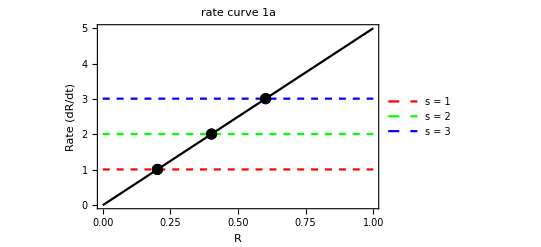

```mathematica
pt1 = ListPlot[inter1, PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[p1,pt1]
```

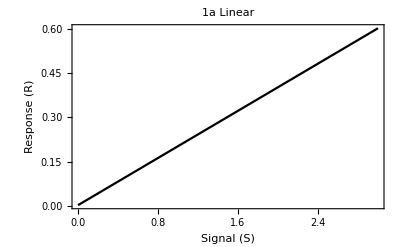

```mathematica
Plot[r[t] /. sol1 /. set1a, {s,0,3},Frame->True, PlotRange->All, FrameLabel->{"Signal (S)","Response (R)"},PlotStyle->Black,PlotLabel->"1a Linear",LabelStyle->{GrayLevel[0]},Axes->True](*Signal Response curve*)
```

Exercise 2

```mathematica
set1b = {k1 -> 1, k2 -> 1, rt -> 1};
D[rp[t],t] == k1 s  (rt -  rp[t]) -k2 rp[t]
pro2 := k1 s (rt -  rp[t]);
deg2 := -k2 rp[t];
```

rp'[t]==k1 s (rt-rp[t])-k2 rp[t]

```mathematica
sol2 = Solve[pro2 == -deg2, rp[t]]
rp[t]/. sol2 /. set1b
```

{{rp[t]→(k1 rt s)/(k2+k1 s)}}

{s/(1+s)}

```mathematica
p2 = Plot[{(pro2 /. set1b) /. s -> 2, (pro2 /. set1b) /. s -> 4, (pro2 /. set1b) /. s -> 8, -deg2 /. set1b}, {rp[t], 0, 1}, Frame -> True, PlotRange-> {0,2}, PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Full, Black}}, PlotLegends->{"s = 2","s = 4","s = 8"},FrameLabel->{"Rp","Rate (dRp/dt)"},PlotLabel->"rate curve 1b",LabelStyle->{GrayLevel[0]},Axes->True];
```

```mathematica
inter2 = {{rp[t],pro2} /. sol2 /. set1b /. s -> 2,{rp[t],pro2} /. sol2 /. set1b /. s -> 4,{rp[t],pro2} /. sol2 /. set1b /. s -> 8}
```

{{{2/3,2/3}},{{4/5,4/5}},{{8/9,8/9}}}

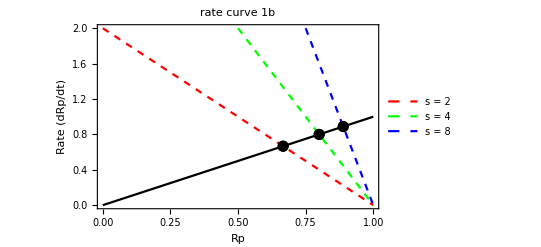

```mathematica
pt2 = ListPlot[inter2, PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[p2,pt2]
```

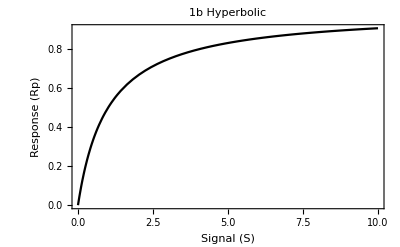

```mathematica
Plot[rp[t] /. sol2 /. set1b, {s,0,10},Frame->True, PlotRange->All, FrameLabel->{"Signal (S)","Response (Rp)"},PlotStyle->Black,PlotLabel->"1b Hyperbolic",LabelStyle->{GrayLevel[0]},Axes->True](*Signal Response curve*)
```

Exercise 3

```mathematica
set1c = {k1->1, k2->1 , rt-> 1, km1-> 0.05, km2->0.05 };
D[rp[t],t] == k1 s (rt - rp[t])/(km1+ rt - rp[t])-k2 rp[t]/(km2+rp[t])
pro3 := k1 s (rt - rp[t])/(km1+ rt - rp[t])
deg3 := -k2 rp[t]/(km2+rp[t])
```

rp'[t]==(k1 s (rt-rp[t]))/(km1+rt-rp[t])-(k2 rp[t])/(km2+rp[t])

```mathematica
sol3 = Solve[pro3 == -deg3, rp[t]]
rp[t]/. sol3 /. set1c
```

{{rp[t]→1/(2 (k2-k1 s))(k2 km1+k2 rt+k1 km2 s-k1 rt s+√(-4 k1 km2 rt s (k2-k1 s)+(-k2 km1-k2 rt-k1 km2 s+k1 rt s)^2))},{rp[t]→1/(2 (-k2+k1 s))(-k2 km1-k2 rt-k1 km2 s+k1 rt s+√(-4 k1 km2 rt s (k2-k1 s)+(-k2 km1-k2 rt-k1 km2 s+k1 rt s)^2))}}

{(1.05-0.95 s+√((-1.05+0.95 s)^2-0.2 (1-s) s))/(2 (1-s)),(-1.05+0.95 s+√((-1.05+0.95 s)^2-0.2 (1-s) s))/(2 (-1+s))}

```mathematica
p3 = Plot[{(pro3 /. set1c) /. s -> 0.25, (pro3 /. set1c) /. s -> 0.5, (pro3 /. set1c) /. s -> 1,(pro3 /. set1c) /. s -> 1.5, (pro3 /. set1c) /. s -> 2, -deg3 /. set1c}, {rp[t], 0, 1}, Frame -> True, PlotRange->All, PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Pink},{Dashed,Cyan},{Full, Black}}, PlotLegends->{"s = 0.25","s = 0.5","s = 1","s = 1.5","s = 2"},FrameLabel->{"Rp","Rate (dRp/dt)"},PlotLabel->"rate curve 1c",LabelStyle->{GrayLevel[0]},Axes->True];
```

```mathematica
inter3 = {{rp[t],pro3} /. sol3[[2]] /. set1c /. s -> 0.25,{rp[t],pro3} /. sol3[[2]] /. set1c /. s -> 0.5,{rp[t],pro3} /. sol3[[2]] /. set1c /. s -> 1.0000000000001,{rp[t],pro3} /. sol3[[2]] /. set1c /. s -> 1.5,{rp[t],pro3} /. sol3[[2]] /. set1c /. s -> 2}
(*If s=1 the denominator is zero. Then in order to plot the intersect a number that is slightly larger than 1 is used.*)
```

{{0.0156095,0.237916},{0.0452595,0.475118},{0.5,0.909091},{0.914096,0.948138},{0.954741,0.950236}}

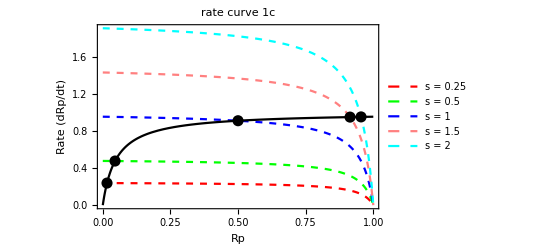

```mathematica
pt3 = ListPlot[inter3, PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[p3,pt3]
```

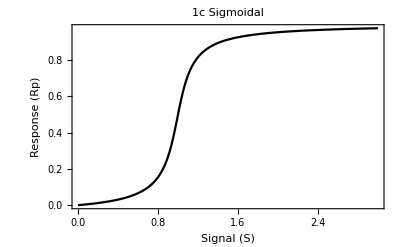

```mathematica
Plot[rp[t] /. sol3[[2]] /. set1c, {s,0,3},Frame->True, PlotRange->All, FrameLabel->{"Signal (S)","Response (Rp)"},PlotStyle->Black,PlotLabel->"1c Sigmoidal",LabelStyle->{GrayLevel[0]},Axes->True](*Signal Response curve*)
```

Exercise 4

```mathematica
set1d = {k1 -> 2, k2 -> 2, k3 -> 1, k4-> 1};
D[r[t],t]== k1 s - k2 x[t]*r[t]
D[x[t],t] == k3 s - k4 x[t]
pro4 := k1 s;
deg4 := -k2 x[t]*r[t];
```

r'[t]==k1 s-k2 r[t] x[t]

x'[t]==k3 s-k4 x[t]

```mathematica
xss4 = Solve[k3 s - k4 x[t] == 0,x[t]]
```

{{x[t]→(k3 s)/k4}}

```mathematica
p4 = Plot[{(pro4 /. set1d) /. s -> 1, (pro4 /. set1d) /. s -> 2, (pro4 /. set1d) /. s -> 3, (-deg4 /.xss4[[1]] /. set1d) /. s -> 1,(-deg4 /.xss4[[1]] /. set1d) /. s -> 2,(-deg4 /.xss4[[1]] /. set1d) /. s -> 3 }, {r[t], 0, 2}, Frame -> True, PlotRange->{0,8}, PlotStyle->{{Dashed,Red},{Dashed,Blue},{Dashed,Green},{Red},{Blue},{Green}}, PlotLegends->{"s = 1","s = 2","s = 3"},FrameLabel->{"R","Rate (dR/dt)"},PlotLabel->"rate curve 1d",LabelStyle->{GrayLevel[0]},Axes->True];
```

```mathematica
sol4 = Solve[pro4 == -deg4 /. xss4[[1]], r[t]]
```

{{r[t]→(k1 k4)/(k2 k3)}}

```mathematica
inter4 = {{r[t],pro4} /. sol4 /. set1d /. s -> 1,{r[t],pro4} /. sol4 /. set1d /. s -> 2,{r[t],pro4} /. sol4 /. set1d /. s -> 3}
```

{{{1,2}},{{1,4}},{{1,6}}}

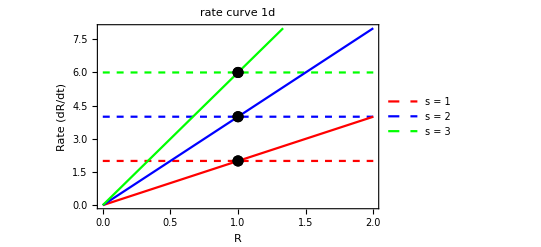

```mathematica
pt4 = ListPlot[inter4, PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[p4,pt4]
```

```mathematica
sig[t_] := IntegerPart[t/4]
```

```mathematica
sys :={D[r[t],t]== k1 sig[t] - k2 x[t]*r[t],D[x[t],t] == k3 sig[t] - k4 x[t]}
sysini = {r[0] == 1.0, x[0] == 0};
```

```mathematica
nsol4 = NDSolve[Join[sys,sysini] /. set1d,{r[t],x[t]},{t,0,20}]
```

{{r[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t]}}

```mathematica
p4 = Plot[{(x[t] /. nsol4)*7/40 + 1.1,sig[t]*7/40+1.1},{t,0,20},PlotStyle-> {Green,Red},ExclusionsStyle -> Red,PlotRange->{0.9,2}, Frame -> True,Axes -> False, PlotLegends->{"X","S"},FrameTicks->{{Automatic,Table[{i,(i-1.1)*40/7},{i,1.1-0.175,1.975,0.7/4}]},{Automatic,None}},PlotLabel-> "Adapted", Frame-> True, FrameLabel->{"Time","Response R"} ];
(*Reference Seting frame ticks: https://mathematica.stackexchange.com/questions/5369/about-the-number-format-in-ticks*)
(*I rescale the plot manually in order to fit the Response curve by *7/40 +1.1, and then manually set the ticks on the right hand side *)
```

```mathematica
pr4 = Plot[r[t] /. nsol4,{t,0,20},PlotRange->{0.9,2.0},PlotStyle->Black,PlotLabel-> "Adapted", Frame-> True, FrameLabel->{"Time","Response R"} ];
```

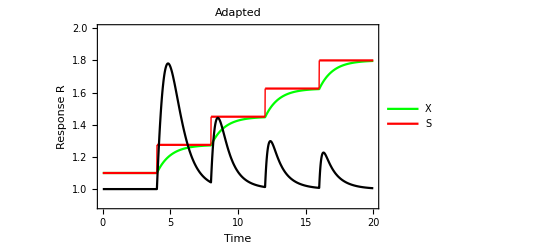

```mathematica
Show[p4,pr4]
```

Exercise 5

```mathematica
G[u_,v_,j_,k_]:= 2 u k /(v - u + v j + u k + Sqrt[(v - u + v j + u k)^2 - 4 (v - u) u k])
```

```mathematica
set1e = {k0 -> 0.4, k1-> 0.01, k2-> 1, k3-> 1, k4-> 0.2, j3-> 0.05, j4-> 0.05};
D[r[t],t]== k0 Ep[r[t]] + k1 s - k2 x[t]r[t]
Ep[r[t]] = G[k3 r[t],k4,j3,j4]
```

r'[t]==k1 s+k0 Ep[r[t]]-k2 r[t] x[t]

(2 j4 k3 r[t])/(k4+j3 k4-k3 r[t]+j4 k3 r[t]+√(-4 j4 k3 r[t] (k4-k3 r[t])+(k4+j3 k4-k3 r[t]+j4 k3 r[t])^2))

```mathematica
pro5 := k0 Ep[r[t]] + k1 s
deg5 := k2 x[t]r[t]
```

```mathematica
sol5 = Solve[pro5 == -deg5 /. x[t] -> 1, r[t]];
```

```mathematica
r[t]/. sol5 /. set1e
```

{1/3 (-0.18-0.02 s)-(2^(1/3) (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2)))/(3 (-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3+√((-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3)^2+4 (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2))^3))^(1/3))+1/(3 2^(1/3))(-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3+√((-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3)^2+4 (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2))^3))^(1/3),1/3 (-0.18-0.02 s)+((1+ⅈ √3) (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2)))/(3 2^(2/3) (-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3+√((-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3)^2+4 (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2))^3))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3+√((-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3)^2+4 (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2))^3))^(1/3),1/3 (-0.18-0.02 s)+((1-ⅈ √3) (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2)))/(3 2^(2/3) (-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3+√((-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3)^2+4 (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2))^3))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3+√((-0.160704+0.001908 s+0.000234 s^2+2.×10^-6 s^3)^2+4 (-(-0.18-0.02 s)^2+3 (-0.092-0.0002 s+0.0001 s^2))^3))^(1/3)}

```mathematica
f0 = (pro5 /. set1e) /. s -> 0;
f8 = (pro5 /. set1e) /. s -> 8;
f16 = (pro5 /. set1e) /. s -> 16;
ff = (deg5 /. set1e) /. x[t] -> 1;
```

```mathematica
p5 = Plot[{f0,f8,f16,ff}, {r[t], 0, 0.7}, Frame -> True, PlotRange-> {0,0.6}, PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Full,Black}}, PlotLegends->{"s = 0","s = 8","s = 16"},FrameLabel->{"R","Rate (dR/dt)"},PlotLabel->"rate curve 1e",LabelStyle->{GrayLevel[0]},Axes->True];
```

```mathematica
solx = Solve[f8 == ff,r[t]]
```

{{r[t]→0.0971492},{r[t]→0.176626},{r[t]→0.466224}}

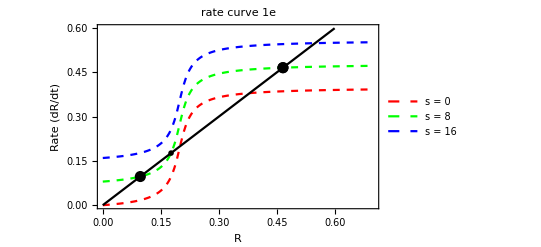

```mathematica
pt5 = ListPlot[{{{r[t]/. solx[[1]],f8 /. solx[[1]]},{r[t]/. solx[[3]],f8 /. solx[[3]]}},{r[t]/. solx[[2]],f8 /. solx[[2]]}},PlotStyle->{{Black,AbsolutePointSize[8]},{Black,AbsolutePointSize[8]}}, PlotMarkers->"OpenMarkers"];
ptt5 = ListPlot[{{{r[t]/. solx[[1]],f8 /. solx[[1]]},{r[t]/. solx[[3]],f8 /. solx[[3]]}}},PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[p5,pt5,ptt5]
(*The filled circle are stable. The not filled circle is unstable.*)
```

```mathematica
sol55 = Solve[pro5 == deg5 /. x[t] -> 1, r[t]];
```

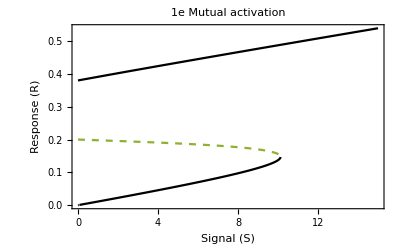

```mathematica
Plot[{r[t] /. sol55[[1]] /. set1e,r[t] /. sol55[[2]] /. set1e,r[t] /. sol55[[3]] /. set1e} , {s,0,15},Frame->True, PlotRange->All, FrameLabel->{"Signal (S)","Response (R)"},PlotStyle->{Black,Black,Dashed},PlotLabel->"1e Mutual activation",LabelStyle->{GrayLevel[0]},Axes->True]
```

Exercise 6

```mathematica
set1g = {k0->1, k2-> 1, k3-> 0.5, k4-> 1, j3-> 0.01, j4-> 0.01};
D[r[t],t]== k0 e[r[t]] - k2 s r[t]
e[r[t]] = G[k3,k4 r[t],j3,j4]
```

r'[t]==-k2 s r[t]+(2 j4 k0 k3)/(-k3+j4 k3+k4 r[t]+j3 k4 r[t]+√(-4 j4 k3 (-k3+k4 r[t])+(-k3+j4 k3+k4 r[t]+j3 k4 r[t])^2))

(2 j4 k3)/(-k3+j4 k3+k4 r[t]+j3 k4 r[t]+√(-4 j4 k3 (-k3+k4 r[t])+(-k3+j4 k3+k4 r[t]+j3 k4 r[t])^2))

```mathematica
pro6 := k0 e[r[t]]
deg6 := - k2 s r[t]
```

```mathematica
sol6 = Solve[pro6 == -deg6, r[t]];
r[t]/. sol6 /. set1g /. s -> 1
```

{1.01981+0. ⅈ,-0.00980579+0. ⅈ,0.5+0. ⅈ}

```mathematica
temp = (pro6 /. set1g) /. s -> 1
```

0.01/(-0.495+1.01 r[t]+√(-0.02 (-0.5+r[t])+(-0.495+1.01 r[t])^2))

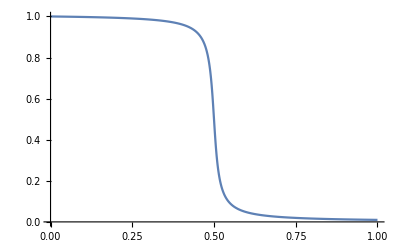

```mathematica
Plot[temp,{r[t],0,1}]
```

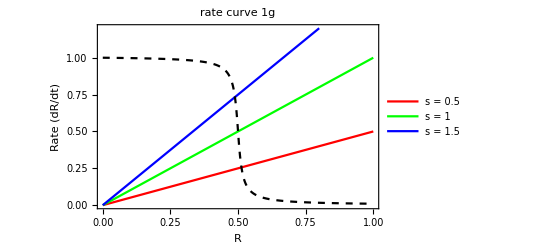

```mathematica
p6 = Plot[{-deg6 /. set1g /. s->0.5,-deg6 /. set1g /. s->1,-deg6 /. set1g /. s->1.5,temp},  {r[t], 0, 1}, Frame -> True, PlotRange->{0,1.2},PlotStyle->{{Full,Red},{Full,Green},{Full,Blue},{Dashed,Black}},PlotLegends->{"s = 0.5","s = 1","s = 1.5"},FrameLabel->{"R","Rate (dR/dt)"},PlotLabel->"rate curve 1g",LabelStyle->{GrayLevel[0]},Axes->True]
```

```mathematica
inter6 = {{r[t],pro6} /. sol6[[3]] /. set1g /. s -> 0.5,{r[t],pro6} /. sol6[[3]] /. set1g /. s -> 1,
{r[t],pro6} /. sol6[[3]] /. set1g /. s -> 1.5}
```

{{0.512615-2.22045×10^-16 ⅈ,0.256307+2.91738×10^-15 ⅈ},{0.5+0. ⅈ,0.5+0. ⅈ},{0.488539+0. ⅈ,0.732808+0. ⅈ}}

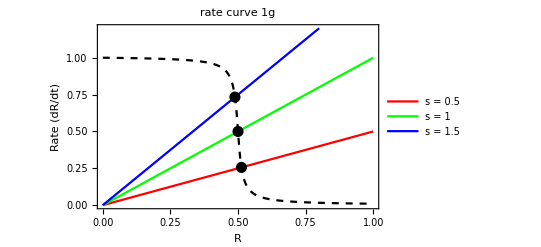

```mathematica
pt6 = ListPlot[inter6, PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[p6,pt6]
```

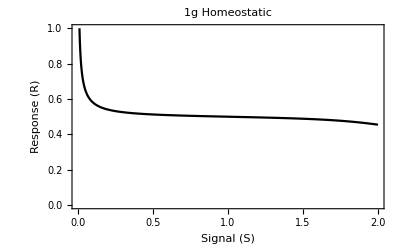

```mathematica
Plot[r[t] /. sol6[[3]] /. set1g, {s,0,2},Frame->True, PlotRange-> {0,1}, FrameLabel->{"Signal (S)","Response (R)"},PlotStyle->Black,PlotLabel->"1g Homeostatic",LabelStyle->{GrayLevel[0]},Axes->False](*Signal Response curve*)
```

Exercise 7

```mathematica
set2b = {k0 -> 4, k1-> 1, k2-> 1,k2'-> 1, k3-> 1, k4-> 1, k5->0.1,k6-> 0.075, j3-> 0.3, j4-> 0.3};
D[r[t],t]== k0 Ep[r[t]] + k1 s - k2 r[t] -k2' x[t]r[t]
D[x[t],t] == k5 r[t] - k6 x[t]
Ep[r[t]] = G[k3 r[t],k4 ,j3,j4]
```

r'[t]==k1 s-k2 r[t]+(2 j4 k0 k3 r[t])/(k4+j3 k4-k3 r[t]+j4 k3 r[t]+√(-4 j4 k3 r[t] (k4-k3 r[t])+(k4+j3 k4-k3 r[t]+j4 k3 r[t])^2))-r[t] x[t] k2'

x'[t]==k5 r[t]-k6 x[t]

(2 j4 k3 r[t])/(k4+j3 k4-k3 r[t]+j4 k3 r[t]+√(-4 j4 k3 r[t] (k4-k3 r[t])+(k4+j3 k4-k3 r[t]+j4 k3 r[t])^2))

```mathematica
pro7:= k0 Ep[r[t]] + k1 s
```

```mathematica
deg7 := - k2 r[t] -k2' x[t]r[t]
```

```mathematica
xss7 = Solve[k5 r[t] - k6 x[t] == 0,x[t]]
```

{{x[t]→(k5 r[t])/k6}}

```mathematica
sol7 = Solve[pro7 == -deg7 /. xss7[[1]], r[t]];
```

```mathematica
sys7 :={D[r[t],t]== k0 Ep[r[t]] + k1 *0.2 - k2 r[t] -k2' x[t]r[t],D[x[t],t] == k5 r[t] - k6 x[t]}
sys7ini = {r[0] == 0, x[0] == 0};
```

```mathematica
nsol7 = NDSolve[Join[sys7,sys7ini] /. set2b,{r[t],x[t]},{t,0,20}]
```

{{r[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t]}}

```mathematica
(* Plot[(r[t] /. nsol4),{x[t],0,1.5},PlotStyle-> {Green,Red},ExclusionsStyle -> Red,PlotRange->{0.9,2}, Frame -> True,Axes -> False, PlotLegends->{"X","S"},FrameTicks->{{Automatic,Table[{i,(i-1.1)*40/7},{i,1.1-0.175,1.975,0.7/4}]},{Automatic,None}},PlotLabel-> "Adapted", Frame-> True, FrameLabel->{"Time","Response R"} ];*)
```

```mathematica
r[t] /. nsol7
```

{InterpolatingFunction[…][t]}

```mathematica
x[t]/. nsol7
```

{InterpolatingFunction[…][t]}

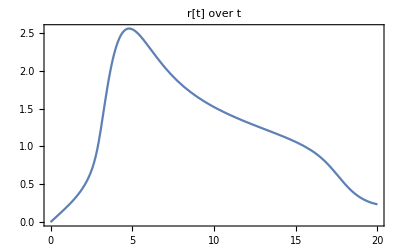

```mathematica
Plot[r[t] /. nsol7,{t,0,20}, Frame -> True,LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> All,PlotLabel->"r[t] over t"]
```

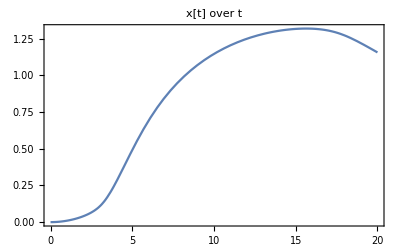

```mathematica
Plot[x[t] /. nsol7,{t,0,20}, Frame -> True,LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> All,PlotLabel->"x[t] over t"]
```

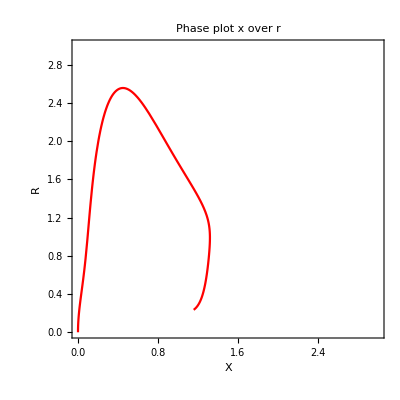

```mathematica
pl =ParametricPlot[Evaluate[{x[t],r[t]}/.nsol7],{t,0,20},PlotRange->{0,3},PlotStyle->Red,PlotLabel->"Phase plot x over r",Frame -> True, FrameLabel->{"X","R"}]
```

```mathematica
Ep[r] = G[k3 r,k4 ,j3,j4]
```

(2 j4 k3 r)/(k4+j3 k4-k3 r+j4 k3 r+√(-4 j4 k3 r (k4-k3 r)+(k4+j3 k4-k3 r+j4 k3 r)^2))

```mathematica
f[r_,x_] = k0 Ep[r] + k1 s - k2 r -k2' x r
g[r_,x_] =  k5 r - k6 x
```

-k2 r+(2 j4 k0 k3 r)/(k4+j3 k4-k3 r+j4 k3 r+√(-4 j4 k3 r (k4-k3 r)+(k4+j3 k4-k3 r+j4 k3 r)^2))+k1 s-r x k2'

k5 r-k6 x

```mathematica
ff[r_,x_] = f[r,x] /. set2b /. s -> 0.2
gg[r_,x_] = g[r,x] /. set2b
```

0.2-r+(2.4 r)/(1.3-0.7 r+√((1.3-0.7 r)^2-1.2 (1-r) r))-r x

0.1 r-0.075 x

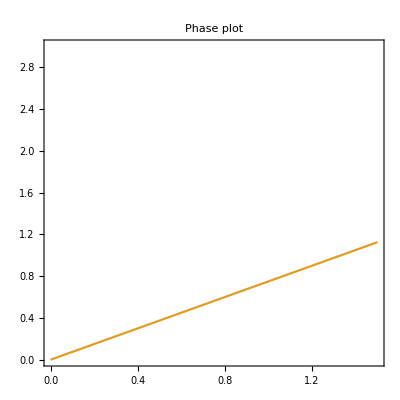

```mathematica
cp=ContourPlot[{ff[r,x]==0,gg[r,x]==0},{x,0,1.5},{r,0,3}, PlotLabel-> Phase plot]
```

```mathematica
cub = NSolve[ff[r,x]==0,r]
```

{{r→-(0.333333 (-105.-130. x-25. x^2))/(25.+50. x+25. x^2)+((0.209987-0.363708 ⅈ) (-8400.-11550. x+1475. x^2+4000. x^3-625. x^4))/((25.+50. x+25. x^2) (1.944×10^6+4.437×10^6 x+1.25325×10^6 x^2-3.391×10^6 x^3-2.4825×10^6 x^4-300000. x^5+31250. x^6+422187. √(12.4711-1. x) √(-1.23036+1. x) √(-0.770424+1. x) √(0.668379+1. x) (1.+1. x)^3)^(1/3))-1/(25.+50. x+25. x^2)(0.132283+0.229122 ⅈ) (1.944×10^6+4.437×10^6 x+1.25325×10^6 x^2-3.391×10^6 x^3-2.4825×10^6 x^4-300000. x^5+31250. x^6+422187. √(12.4711-1. x) √(-1.23036+1. x) √(-0.770424+1. x) √(0.668379+1. x) (1.+1. x)^3)^(1/3)},{r→-(0.333333 (-105.-130. x-25. x^2))/(25.+50. x+25. x^2)+((0.209987+0.363708 ⅈ) (-8400.-11550. x+1475. x^2+4000. x^3-625. x^4))/((25.+50. x+25. x^2) (1.944×10^6+4.437×10^6 x+1.25325×10^6 x^2-3.391×10^6 x^3-2.4825×10^6 x^4-300000. x^5+31250. x^6+422187. √(12.4711-1. x) √(-1.23036+1. x) √(-0.770424+1. x) √(0.668379+1. x) (1.+1. x)^3)^(1/3))-1/(25.+50. x+25. x^2)(0.132283-0.229122 ⅈ) (1.944×10^6+4.437×10^6 x+1.25325×10^6 x^2-3.391×10^6 x^3-2.4825×10^6 x^4-300000. x^5+31250. x^6+422187. √(12.4711-1. x) √(-1.23036+1. x) √(-0.770424+1. x) √(0.668379+1. x) (1.+1. x)^3)^(1/3)},{r→-(0.333333 (-105.-130. x-25. x^2))/(25.+50. x+25. x^2)-(0.419974 (-8400.-11550. x+1475. x^2+4000. x^3-625. x^4))/((25.+50. x+25. x^2) (1.944×10^6+4.437×10^6 x+1.25325×10^6 x^2-3.391×10^6 x^3-2.4825×10^6 x^4-300000. x^5+31250. x^6+422187. √(12.4711-1. x) √(-1.23036+1. x) √(-0.770424+1. x) √(0.668379+1. x) (1.+1. x)^3)^(1/3))+1/(25.+50. x+25. x^2)0.264567 (1.944×10^6+4.437×10^6 x+1.25325×10^6 x^2-3.391×10^6 x^3-2.4825×10^6 x^4-300000. x^5+31250. x^6+422187. √(12.4711-1. x) √(-1.23036+1. x) √(-0.770424+1. x) √(0.668379+1. x) (1.+1. x)^3)^(1/3)}}

```mathematica
cub /. x -> 0
```

{{r→0.143631+0.505363 ⅈ},{r→0.143631-0.505363 ⅈ},{r→3.91274+0. ⅈ}}

```mathematica
cub /. x-> 0.5
```

{{r→0.340742+0.282251 ⅈ},{r→0.340742-0.282251 ⅈ},{r→2.45185+0. ⅈ}}

```mathematica
cub /. x-> 1
```

{{r→0.754042+4.44089×10^-16 ⅈ},{r→0.220256-2.22045×10^-16 ⅈ},{r→1.6257-1.66533×10^-16 ⅈ}}

```mathematica
cub /. x-> 1.5
```

{{r→1.07239+0.35773 ⅈ},{r→0.135211-4.85723×10^-17 ⅈ},{r→1.07239-0.35773 ⅈ}}

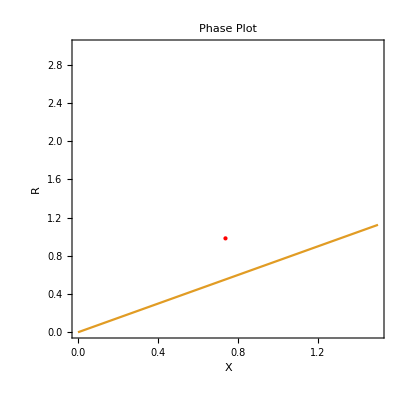

```mathematica
ptRules=NSolve[{ff[r,x]==0,gg[r,x]==0},{r,x}];
Show[cp,Graphics[{Red,PointSize[Large],Point[{r,x}]/.Cases[ptRules,n_List /; ( Element[({r,x}/. n)[[1]],Reals]&& Element[({r,x}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[R],None},{HoldForm[X],None}},PlotLabel->HoldForm[Phase Plot],LabelStyle->{GrayLevel[0]},Axes->True]
```

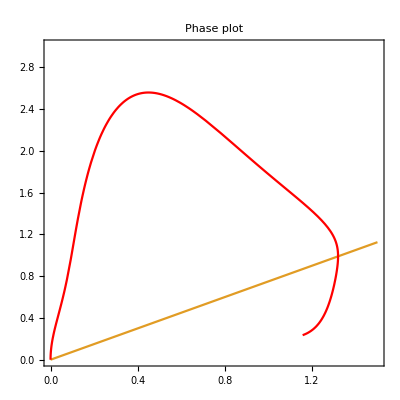

```mathematica
Show[cp,pl]
```

```mathematica
Plot[r[t] /. nsol7 /. set2b, {s,0,1},Frame->True, PlotRange-> {0,1}, FrameLabel->{"Signal (S)","Response (R)"},PlotStyle->Black,PlotLabel->"2b Signal Response curve",LabelStyle->{GrayLevel[0]},Axes->False]
```

-Graphics-

I do not feel I get the last exercise. I have tried to draw the phase plot with ContourPlot, but only the linear nucline shows up, I wander why the cubic one does not show up? I have also tried ParametricPlot, but not sure what does the output mean.